```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
c=299792.458"km"/"s";
AutoPlotRegends[params_List]:=ToString[#/.Rule[a_,b_]:>ToString[a]<>"="<>ToString[b]]//.x_List:>StringJoin[Riffle[x,", "]]&/@params
```

```mathematica
(* distance modules *)
μ[z_,Ωm_,H0_]:=25+5Log10[DL[z,Ωm,H0]/("Mpc")]
(* luminosity distance *)
DL[z_,Ωm_,H0_]:=c/H0(1+z)(η[1,Ωm]-η[1/(1+z),Ωm])
η[a_,Ωm_]:=Module[{s=((1-Ωm)/Ωm)^(1/3)},
2 √(s^3+1)(1/a^4-0.1540 s/a^3+0.4304 s^2/a^2+0.19097 s^3/a+0.066941 s^4)^(-1/8)]
Data=Select[Import["SN.txt","Table"],Length[#]==5&][[2;;]];
Data=Select[Data,#[[2]]<1.8&];
Data//Length
```

292

```mathematica
LogL[{Ωm_,h_}]:=-1/2 Total[(#[[3]]-μ[#[[2]],Ωm,100h("km")/("s""Mpc")])^2/((#[[4]])^2+0.1^2)&/@Data]
```

#### With a “Top-hat” (rectangle) proposal distribution

```mathematica
RandDistance=100;
NextRand[{Ωm_,h_}]:=RandomReal[{#-RandDistance/2,#+RandDistance/2}]&/@{Ωm,h}
NextPoint[old_]:=Module[{new=NextRand[old],acceptance},
acceptance=Exp[LogL[new]-LogL[old]];
If[Im[acceptance]≠0,Print[new,old]];
If[RandomReal[]<acceptance,new,old]];
NestList[NextPoint,{RandomReal[],RandomReal[]},100];
ListPlot[%,Joined->True]
```

{30.7244,-36.6225}{0.38156,0.910225}

Less::nord: Invalid comparison with 2.25740134724903×10^-106740 - 3.10310721502606×10^-106741\ ⅈ attempted.

$Aborted

ListPlot::lpn: $Aborted is not a list of numbers or pairs of numbers.

ListPlot[$Aborted,Joined→True]

#### The values should be between 0.01 and 0.99; rectangle proposal distribution.

```mathematica
q[new_,old_]:=If[And@@(0.01<#<0.99&/@new),1,0]
(*therefore*)
qoverq[new_,old_]:=If[And@@(0.01<#<0.99&/@new),1,0]

NextPoint$last={Null,Null};
NextPoint[old_]:=Module[{new=NextRand[old],LogLold,LogLnew,acceptance},
LogLold=If[NextPoint$last[[1]]===old,NextPoint$last[[2]],LogL[old]];
LogLnew=LogL[new];
acceptance=Exp[LogLnew-LogLold]qoverq[new,old];
If[RandomReal[]<acceptance,
NextPoint$last={new,LogLnew};new,
old]];
```

#### Extreme values for the distance

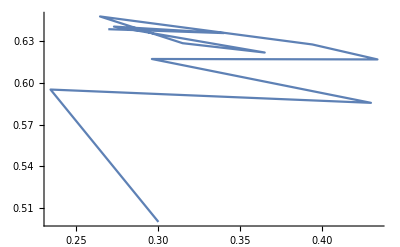

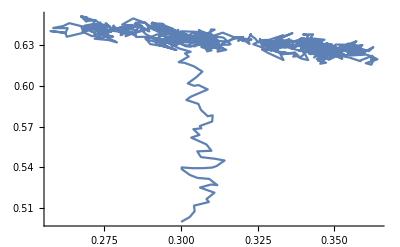

```mathematica
RandDistance=0.5;
ListPlot[NestList[NextPoint,{0.3,0.5},1000],Joined->True,PlotRange->{All,All}]

RandDistance=0.01;
ListPlot[NestList[NextPoint,{0.3,0.5},1000],Joined->True,PlotRange->{All,All}]
```

#### MC chain

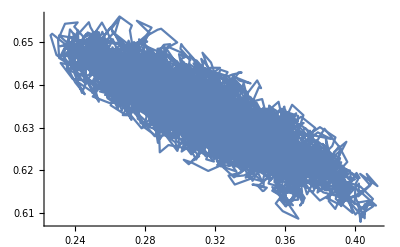

```mathematica
NextRand[{Ωm_,h_}]:={RandomReal[{Ωm-0.01,Ωm+0.01}],RandomReal[{h-0.005,h+0.005}]}
initial=Nest[NextPoint,{RandomReal[],RandomReal[]},1000];
MCchain=NestList[NextPoint,initial,10000];
ListPlot[MCchain,Joined->True]
```

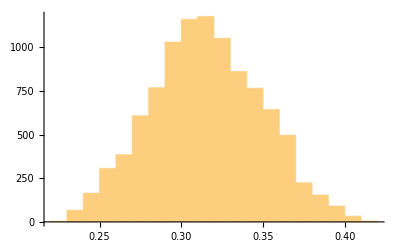

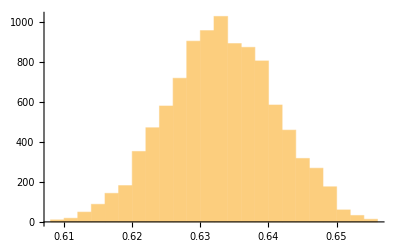

```mathematica
Histogram[MCchain[[All,1]]]
Histogram[MCchain[[All,2]]]
```

```mathematica
Mean[MCchain]
Variance[MCchain]//Sqrt
```

{0.315176,0.633039}

{0.0336738,0.00788464}

#### Gelman--Rubin test

Formulae taken from SAS/STAT(R) 13.2 User’s Guide
http://support.sas.com/documentation/cdl/en/statug/67523/HTML/default/viewer.htm#statug_introbayes_sect024.htm#statug.introbayes.a0000000073

```mathematica
GBtest[chains_]:=
Module[
{
n=Length[chains[[1]]],
M=Length[chains],
θm=Mean/@chains,
θ,B,W,V},
If[DeleteDuplicates[Length/@chains]=!={n},Print["MCchains not same length"];Abort[]];
θ=Mean[θm];
B=n/(M-1)Total[(#-θ)^2&/@θm];
W=Mean[Variance/@chains];
V=(n-1)/n W+(M+1)/(n M)B;
{V/W}]
```

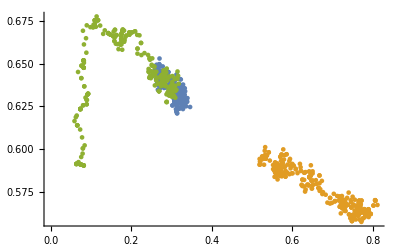

{{16.379,9.83429}}

```mathematica
RandDistance=0.1;
MCchains=Table[
initial=Nest[NextPoint,{RandomReal[],RandomReal[]},100];
NestList[NextPoint,initial,300],{3}];
ListPlot[MCchains]
GBtest[MCchains]
```

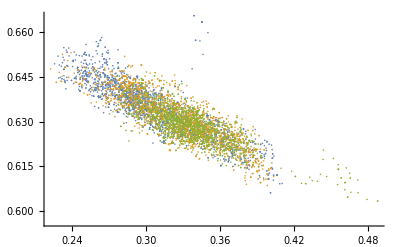

{{1.48483,1.28803}}

```mathematica
RandDistance=0.01;
MCchains=Table[
initial=Nest[NextPoint,{RandomReal[],RandomReal[]},100];
NestList[NextPoint,initial,2000],{3}];
ListPlot[MCchains]
GBtest[MCchains]
```

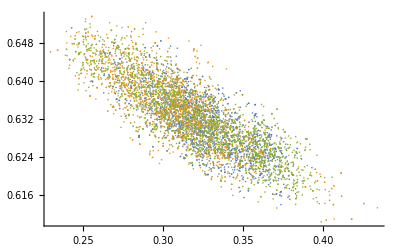

{{1.14108,1.08969}}

```mathematica
RandDistance=0.05;
MCchains=Table[
initial=Nest[NextPoint,{RandomReal[],RandomReal[]},100];
NestList[NextPoint,initial,2000],{3}];
ListPlot[MCchains]
GBtest[MCchains]
```